## Stringy AdS wormholes: type IIB on T^(1,1)

## 10D Einstein frame

### Ansatz

```mathematica
coord={r,θ1,θ2,θ3,θ4,ϑ1,φ1,ϑ2,φ2,ψ};
metric5=DiagonalMatrix@Flatten@{f[r]^2,q[r]^2{1,Sin[θ1]^2{1,Sin[θ2]^2{1,Sin[θ3]^2}}}};
metricT11=1/6 ⅇ^(2u[r])({{1, 0, 0, 0, 0}, {0, Sin[ϑ1]^2, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, Sin[ϑ2]^2, 0}, {0, 0, 0, 0, 0}})+1/9 ⅇ^(2v[r])({{0, 0, 0, 0, 0}, {0, Cos[ϑ1]^2, 0, Cos[ϑ1]Cos[ϑ2], Cos[ϑ1]}, {0, 0, 0, 0, 0}, {0, Cos[ϑ1]Cos[ϑ2], 0, Cos[ϑ2]^2, Cos[ϑ2]}, {0, Cos[ϑ1], 0, Cos[ϑ2], 1}});
metric=ArrayFlatten[{{l^2 ⅇ^(-2/3(4u[r]+v[r]))metric5,0},{0,l^2 metricT11}}];
metricsign=(+1);
$Assumptions=And[f[r]>0,q[r]>0,u[r]∈Reals,v[r]∈Reals,l>0,0<θ1<π,0<θ2<π,0<θ3<π,0<ϑ1<π,0<ϑ2<π];
<<Diffgeo`
```

```mathematica
ws[f_,g_]:=wedge[f,HodgeStar@g];
```

```mathematica
e1=dd[ϑ1];
e2=Sin[ϑ1]dd[φ1];
e3=Cos[ψ]dd[ϑ2]+Sin[ψ]Sin[ϑ2]dd[φ2];
e4=Sin[ψ]dd[ϑ2]-Cos[ψ]Sin[ϑ2]dd[φ2];
e5=dd[ψ]+Cos[ϑ1]dd[φ1]+Cos[ϑ2]dd[φ2];

η=1/3 e5;
Φ2=1/(6 √2)(wedge[e1,e2]+wedge[e3,e4]);
```

```mathematica
vol4=Sin[θ1]^3  Sin[θ2]^2  Sin[θ3] 𝕕[θ1,θ2,θ3,θ4];
vol5=f[r] q[r]^4 Sin[θ1]^3  Sin[θ2]^2  Sin[θ3] 𝕕[r,θ1,θ2,θ3,θ4];
volT11=Simplify[-wedge[Φ2,Φ2,η]];
```

```mathematica
Φ=ϕ[#]+Log[gs]&;
B2=l^2 gs^(1/2)b2[r]Φ2;
C0=I gs^-1 χ[r];
C2=I l^2 gs^(-1/2)c2[r]Φ2;


H3=exterior[B2];
F1=exterior[C0];
F3=exterior[C2]-C0 H3;
F5=4 l^4(volT11-I HodgeStar@volT11);
```

```mathematica
HodgeStar[F5]==I F5//Simplify
```

True

### Equations of motion

#### Matter

```mathematica
exterior@HodgeStar@exterior@Φ[r]-ⅇ^(2Φ[r])ws[F1,F1]+1/2 ⅇ^(-Φ[r])ws[H3,H3]-1/2 ⅇ^Φ[r] ws[F3,F3];
eqnΦ=Simplify[%/(l^-2 ⅇ^(2/3(4u[r]+v[r]))volumeForm)];

exterior[ⅇ^(-Φ[r])HodgeStar@H3]-ⅇ^Φ[r] ws[F1,F3]-ws[F3,F5];
eqnB2=Simplify[%/(gs^(-1/2)ⅇ^(2/3(4u[r]+v[r]))ⅇ^(-ϕ[r])HodgeStar[Φ2])];

exterior[ⅇ^(2Φ[r])HodgeStar@F1]+ⅇ^Φ[r] ws[H3,F3];
eqnC0=Simplify[%/(I l^-2 gs ⅇ^(2/3(4u[r]+v[r]))ⅇ^(2ϕ[r])volumeForm)];

exterior[ⅇ^Φ[r] HodgeStar@F3]+ws[H3,F5];
eqnC2=Simplify[%/(I gs^(1/2)ⅇ^(2/3(4u[r]+v[r]))ⅇ^ϕ[r] HodgeStar@Φ2)];

eqnC4=Simplify[exterior[F5]-wedge[H3,F3]];

(* eqnC4 is automatic *)
eqnC4==0
eqnscalar10D={eqnΦ,eqnB2,eqnC0,eqnC2};
```

True

#### Metric

```mathematica
(* RHS terms for Φ *)
covariant@Φ[r];
WΦ=%**%;

(* RHS terms for Subscript[H, 3] *)
FormToTensor@H3;
raise[%,{2,3}];
raise[%%,{1,2,3}];
WH3=3/(3!)Table[Sum[%%%[[ii,kk,ll]]%%[[jj,kk,ll]],{kk,10},{ll,10}],{ii,10},{jj,10}]-(3-1)/(8 3!)metric Sum[%%%[[ii,jj,kk]]%[[ii,jj,kk]],{ii,10},{jj,10},{kk,10}];

(* RHS terms for Subscript[F, 1] *)
FormToTensor@F1;
WF1=%**%;

(* RHS terms for Subscript[F, 3] *)
FormToTensor@F3;
raise[%,{2,3}];
raise[%%,{1,2,3}];
WF3=3/(3!)Table[Sum[%%%[[ii,kk,ll]]%%[[jj,kk,ll]],{kk,10},{ll,10}],{ii,10},{jj,10}]-(3-1)/(8 3!)metric Sum[%%%[[ii,jj,kk]]%[[ii,jj,kk]],{ii,10},{jj,10},{kk,10}];

(* RHS terms for Subscript[F, 5]: note that Subscript[F, 5]^2==0, which speeds up computation *)
FormToTensor@F5;
raise[%,{2,3,4,5}];
WF5=5/(5!)Table[Sum[%%[[ii,kk,ll,mm,nn]]%[[jj,kk,ll,mm,nn]],{kk,10},{ll,10},{mm,10},{nn,10}],{ii,10},{jj,10}];

(* Einstein equations: by symmetry only four are distinct (r, S^4, KE base and η) *)
l^2 ⅇ^(-2/3(4u[r]+v[r]))raise[RicciTensor-1/2(WΦ+ⅇ^(-Φ[r])WH3+ⅇ^(2Φ[r])WF1+ⅇ^Φ[r] WF3+1/2 WF5),{2}];
eqnmetric10D=Simplify@Expand@{%[[1,1]],%[[2,2]],%[[6,6]],%[[10,10]]};
```

Collect all nontrivial 10D equations of motion.

```mathematica
eqns10D=Flatten@{eqnscalar10D,eqnmetric10D};
Length@eqns10D
```

8

## 5D Einstein frame

```mathematica
Clear[coord,metric5,metricT11,metric,metricsign,e1,e2,e3,e4,e5,η,Φ2,vol4,vol5,volT11,Φ,B2,C0,C2,H3,F1,F3,F5,eqnΦ,eqnB2,eqnC0,eqnC2,eqnC4,eqnscalar10D,WΦ,WH3,WF1,WF3,WF5,eqnmetric10D]
```

### Metric

```mathematica
coord={r,θ1,θ2,θ3,θ4};
metric=DiagonalMatrix@Flatten@{f[r]^2,q[r]^2{1,Sin[θ1]^2{1,Sin[θ2]^2{1,Sin[θ3]^2}}}};
metricsign=+1;
$Assumptions=And[f[r]>0,q[r]>0,r>0,0<θ1<π,0<θ2<π,0<θ3<π];
<<Diffgeo`
```

```mathematica
harmrule={h[r]->h,h'[r]->f[r]/q[r]^4,h''[r]->D[f[r]/q[r]^4,r]};
```

```mathematica
vol4=Sin[θ1]^3 Sin[θ2]^2 Sin[θ3]dd[θ1,θ2,θ3,θ4];
```

### Equations of motion

```mathematica
V[u_,v_]:=2 ⅇ^(-8/3(4u+v))(2 ⅇ^(4u+4v)-12 ⅇ^(6u+2v)+4);
```

#### Scalars

```mathematica
scalarLaplacian@ϕ[r]+1/2 ⅇ^(-4u[r]-ϕ[r])norm@covariant@b2[r]+ⅇ^(2ϕ[r])norm@covariant@χ[r]+1/2 ⅇ^(-4u[r]+ϕ[r])norm[covariant@c2[r]-χ[r]covariant@b2[r]];
eqnϕ=Simplify[%];

exterior[ⅇ^(-4u[r]-ϕ[r])HodgeStar@exterior@b2[r]]+ⅇ^(-4u[r]+ϕ[r])ws[exterior@χ[r],exterior@c2[r]-χ[r]exterior@b2[r]];
eqnb2=Simplify[%/(ⅇ^(-4u[r]-ϕ[r])volumeForm)];

exterior[ⅇ^(2ϕ[r])HodgeStar@exterior@χ[r]]+ⅇ^(-4u[r]+ϕ[r])ws[exterior@b2[r],exterior@c2[r]-χ[r]exterior@b2[r]];
eqnc0=Simplify[%/(ⅇ^(2ϕ[r])volumeForm)];

exterior[ⅇ^(-4u[r]+ϕ[r])HodgeStar[exterior@c2[r]-χ[r]exterior@b2[r]]];
eqnc2=Simplify[%/(ⅇ^(-4u[r]+ϕ[r])volumeForm)];

scalarLaplacian[7u[r]+v[r]]-3/8 D[V[u[r],v[r]], u[r]]+3/4 ⅇ^(-4u[r]-ϕ[r])norm@covariant@b2[r]-3/4 ⅇ^(-4u[r]+ϕ[r])norm[covariant@c2[r]-χ[r]covariant@b2[r]];
eqnu=Simplify[%];

scalarLaplacian[u[r]+v[r]]-3/8 D[V[u[r],v[r]], v[r]];
eqnv=Simplify[%];

eqnscalar={eqnϕ,eqnb2,eqnc0,eqnc2,eqnu,eqnv};
```

#### Metric

```mathematica
(* RHS terms for ϕ *)
covariant@ϕ[r];
Wϕ=%**%;

(* RHS terms for Subscript[F, 1] *)
covariant@χ[r];
Wc0=-%**%;

(* RHS terms for Subscript[H, 3] *)
covariant@b2[r];
Wb2=%**%;

(* RHS terms for Subscript[F, 3] *)
covariant@c2[r]-χ[r]covariant@b2[r];
Wc2=-%**%;

(* RHS terms for u/v *)
covariant@u[r];
covariant@v[r];
Wuv=56/3%%**%%+8/3(%%**%+%**%%)+8/3%**%;


(* Einstein equations: by symmetry only two are distinct *)
raise[RicciTensor-1/2(Wϕ+ⅇ^(-4u[r]-ϕ[r])Wb2+ⅇ^(2ϕ[r])Wc0+ⅇ^(-4u[r]+ϕ[r])Wc2+Wuv)-1/3 metric V[u[r],v[r]],{2}]//Simplify;
eqnmetric={%[[1,1]],%[[2,2]]};
```

Collect all 5D equations of motion.

```mathematica
eqns=Flatten@{eqnscalar,eqnmetric};
Length@eqns
```

8

### Cross-check (5D ↔ 10D)

These 5D equations of motion are equivalent to the 10D equations of motion because they are related by an invertible linear transformation.

```mathematica
L10to5=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -7, -1}, {0, 0, 0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, 1, 0, 4/3, 1/3}, {0, 0, 0, 0, 0, 1, 4/3, 1/3}});
eqns==L10to5.eqns10D//Simplify
Det[L10to5]≠0
```

True

True

```mathematica
Mij=2/(σp-σm)({{σp σm, -(σp+σm)/2}, {-(σp+σm)/2, 1}});
Mijnew=Simplify[Mij/.{σp->(a σp+b)/(c σp+d),σm->(a σm+b)/(c σm+d)}];
```

```mathematica
Solve[a^2+b c e l-a d e l==0,l]
```

{{l→-a^2/((b c-a d) e)}}

```mathematica
U=({{d, c}, {b, a}});
Mijnew==(a d-b c)Transpose[Inverse[U]].Mij.Inverse[U]//Simplify
```

{{d,c},{b,a}}

True

```mathematica
(a d-b c)Inverse[U]
```

{{d,c},{b,a}}

## Solutions

#### “Background” EAdS_5 solution

```mathematica
With[{ϕ=0&,c2=0&,u=0&,v=0&,f=q'[#](1+q[#]^2)^(-1/2)&},Evaluate@{eqns,RicciScalar}]//Simplify
```

{{0,0,0,0,0,0},-20}

### Truncations and “approximations”

Various ad hoc changes to the scalar potential give explicit Giddings-Strominger wormhole solutions when only one flux is turned on. Some are regular and some are singular.
With only H_3-flux or only F_3-flux in one limit (u==v==0 frozen) the WH is regular and in the other (u,v massless) the WH is regular iff the flux is large enough. The true potential is somewhere in between these limits: certainly if the flux is large enough then this will just be some some deformation of the GS solution. If the flux is small the it is not immediately obvious if a regular WH solution exists.

#### u==v==0 frozen: (regular)

If u,v are frozen to zero (artificially), there is a regular wormhole solution.

The solution:

```mathematica
eqns/.{c2'[r]->f3 ⅇ^(4u[r]-ϕ[r])f[r]/q[r]^4,c2''[r]->D[f3 ⅇ^(4u[r]-ϕ[r])f[r]/q[r]^4,r]};
With[{u=0&,v=0&},Evaluate@%];
With[{ϕ=2Log[Cos[1/2 √-c h[#]]/Cos[1/2 √-c h∞]]&},Evaluate@%]/.{h[r]->h,h'[r]->f[r]/q[r]^4,h''[r]->D[f[r]/q[r]^4,r]}//Simplify;
With[{f=q'[#](1+q[#]^2+c/(24 q[#]^6))^(-1/2)&,f3=(√-c)/Cos[1/2 √-c h∞]},Evaluate@%]//Simplify
```

{0,0,(3 c Sec[(√-c h)/2]^2)/(4 q[r]^8),0,0,0}

The range of B h[r] is less than π for all B/h3/q_0:

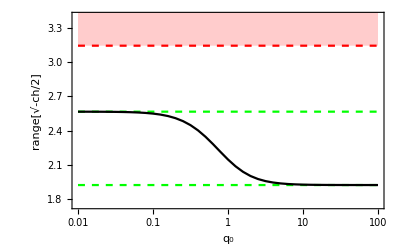

```mathematica
R[q0_]:=2×1/2 √(24 q0^6(1+q0^2))NIntegrate[1/q^4(1+q^2-(q0^6(1+q0^2))/q^6)^(-1/2),{q,q0,∞}];
{#,R@#}&/@(10^Range[-2,2,0.1]);
Show[
LogLinearPlot[{π √(2/3),π √(3/8)},{q0,Min[%[[All,1]]],Max[%[[All,1]]]},PlotStyle->Directive[Green,Dashed]],
LogLinearPlot[π,{q0,Min[%[[All,1]]],Max[%[[All,1]]]},Filling->Top,PlotStyle->Directive[Red,Dashed]],
ListLogLinearPlot[%,Joined->True,PlotStyle->Black],
PlotRange->{1.75,3.4},
Frame->True,
FrameLabel->{"q_0","range[√-ch/2]"},
Background->White,
FrameStyle->Black
]
```

#### (ad hoc) V→-12: (regular iff f_3 is large enough)

```mathematica
dsi={1/(√2)(-4du+dϕ),1/(√2)(4du+dϕ),√(8/3)(du+dv)};
1/2 dsi.dsi-(1/2 dϕ^2+28/3 du^2+8/3 du dv+4/3 dv^2);
Collect[%,{du,dv,dϕ},Simplify]
```

0

If one makes the formal replacement V→-12 (i.e. make u,v massless) then there are AdS wormhole solutions with 4v==-4u=ϕ which can be made explicit.

The solution:

```mathematica
eqns+{0,0,3/8 D[#, u[r]],3/8 D[#, v[r]],1/3#,1/3#}&@(V[u[r],v[r]]+12)//Simplify;
With[{b2=0&,c0=0&},Evaluate@{%,HodgeStar[ⅇ^(-4u[r]+ϕ[r])exterior@c2[r]]/vol4}]//Simplify;
%/.{c2'[r]->f3 ⅇ^(4u[r]-ϕ[r])f[r]/q[r]^4,c2''[r]->D[f3 ⅇ^(4u[r]-ϕ[r])f[r]/q[r]^4,r]};
With[{u=-1/4 ϕ[#]&,v=1/4 ϕ[#]&},Evaluate@%]//Simplify;
With[{ϕ=Log[Cos[1/(√2)√-c h[#]]/Cos[1/(√2)√-c h∞]]&},Evaluate@%]/.{h[r]->h,h'[r]->f[r]/q[r]^4,h''[r]->D[f[r]/q[r]^4,r]}//Simplify;
With[{f=q'[#](1+q[#]^2+c/(24 q[#]^6))^(-1/2)&,f3=(√-c)/Cos[1/(√2)√-c h∞]},Evaluate@%]//Simplify
```

{{0,0,0,0,0,0},√-c Sec[(√-c h∞)/(√2)]}

The range of B h[r] is less than π (giving a regular solution) only if B/f1/q_0 is large enough.

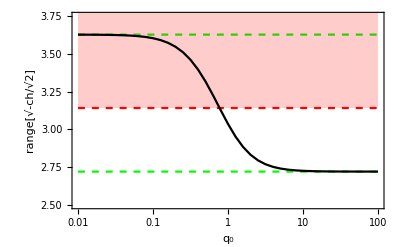

```mathematica
R[q0_]:=2×1/(√2)√(24 q0^6(1+q0^2))NIntegrate[1/q^4(1+q^2-(q0^6(1+q0^2))/q^6)^(-1/2),{q,q0,∞}];
{#,R@#}&/@(10^Range[-2,2,0.1]);
Show[
LogLinearPlot[{(2π)/(√3),π(√3)/2},{q0,Min[%[[All,1]]],Max[%[[All,1]]]},PlotStyle->Directive[Green,Dashed]],
LogLinearPlot[π,{q0,Min[%[[All,1]]],Max[%[[All,1]]]},Filling->Top,PlotStyle->Directive[Red,Dashed]],
ListLogLinearPlot[%,Joined->True,PlotStyle->Black],
PlotRange->{2.5,3.75},
Frame->True,
FrameLabel->{"q_0","range[√-ch/√2]"},
Background->White,
FrameStyle->Black
]
```

In this approximation the GS wormhole is regular everywhere only if the flux (axion charge) is large: only wormholes with minimal radius q_0≳1 are good solutions. This can be understood as follows: if we set -4u==4v==ϕ in the action, we have

ℒ⊃-1/2dϕ⋀⋆dϕ-28/3 du⋀⋆du-8/3 du⋀⋆dv-4/3 dv⋀⋆dv-1/2 ⅇ^(-4u+ϕ)dc_2⋀⋆dc_2
         →-dϕ⋀⋆dϕ-1/2 ⅇ^(2ϕ)dc_2⋀⋆dc_2
         ==-1/2dϕ̃⋀⋆d ϕ̃-1/2 ⅇ^(√2 ϕ̃)dc_2⋀⋆dc_2        where    ϕ̃==√2 ϕ

This is a β==√2 axiodilaton pair and this violates the 5D flat space bound: β^2>β_cr^2==3/2. However, in AdS the bound is somewhat weaker which is exactly what happens for large q_0 where the wormhole is large and the AdS curvature is felt.

### Mass eigenstates/eigenvalues

```mathematica
SeriesCoefficient[V[ϵ u,ϵ v],{ϵ,0,2}]/.k->2;
Vij=Simplify@({{2Coefficient[%,u^2], Coefficient[%,u v]}, {Coefficient[%,u v], 2Coefficient[%,v^2]}});
Tij=8/3({{7, 1}, {1, 1}});
Eigenvalues[Inverse[Tij].Vij]
2+√(4+%)
```

{32,12}

{8,6}

```mathematica
1/2{du,dv}.Tij.{du,dv}-1/2{u,v}.Vij.{u,v};
1/2{(du-dv)/(√(5/8)),(4du+dv)/(√(15/16))}.({{1, 0}, {0, 1}}).{(du-dv)/(√(5/8)),(4du+dv)/(√(15/16))}-1/2{(u-v)/(√(5/8)),(4u+v)/(√(15/16))}.({{12, 0}, {0, 32}}).{(u-v)/(√(5/8)),(4u+v)/(√(15/16))};
%%==%//Simplify
```

True

### Series solutions and shooting method prep (H_3==F_1==0)

Near r==0:

```mathematica
With[{b2=0&,c0=0&},Evaluate@eqns];
%/.{c2'[r]->f3 ⅇ^(4u[r]-ϕ[r])f[r]/q[r]^4,c2''[r]->D[f3 ⅇ^(4u[r]-ϕ[r])f[r]/q[r]^4,r]}//Simplify;
eqnsflux=Drop[%,{2}];
```

```mathematica
f0soln={f0->(3-1/3 q0^2 V[u0,v0])^(-1/2)};
f3soln={f3^2->6 ⅇ^(-4u0+ϕ0)q0^6(1+f0^-2)};
f2soln={f2->(f0^3 q0^2)/12((6(3+f0^-2))/q0^4+u2 D[V[u0,v0], u0]+v2 D[V[u0,v0], v0])};
u2soln={u2->f0^2/16(D[V[u0,v0], u0]-D[V[u0,v0], v0]+(2 f3^2 ⅇ^(4u0-ϕ0))/q0^8)};
v2soln={v2->f0^2/16(-D[V[u0,v0], u0]+7 D[V[u0,v0], v0]-(2 f3^2 ⅇ^(4u0-ϕ0))/q0^8)};
ϕ2soln={ϕ2->-(f0^2 f3^2 ⅇ^(4u0-ϕ0))/(2 q0^8)};
With[{q=√(q0^2+#^2)&,f=f0+1/2 f2 #^2+1/24 f4#^4&,u=u0+1/2 u2#^2+1/24 u4#^4&,v=v0+1/2 v2#^2+1/24 v4#^4&,ϕ=ϕ0+1/2 ϕ2#^2+1/24 ϕ4#^4&},Evaluate@eqnsflux];
%/.f2soln/.u2soln/.v2soln/.ϕ2soln/.f3soln/.f0soln;
Series[{r,r,r,1,1}%,{r,0,2}]//Simplify//Union//Column
```

O[r]^3

```mathematica
prefactorrule={prefactor->q''[r]/q'[r]-q'[r]/q[r]-f[r]^2/(q[r]q'[r])(3-1/3 q[r]^2 V[u[r],v[r]])};
fprime={f'[r]->(prefactor+(4q'[r])/q[r])f[r]};
udprime={ud'[r]->prefactor ud[r]+f[r]^2/16(D[V[u[r],v[r]], u[r]]-D[V[u[r],v[r]], v[r]]+2 (f3^2 ⅇ^(4u[r]-ϕ[r]))/q[r]^8)};
vdprime={vd'[r]->prefactor vd[r]+f[r]^2/16(-D[V[u[r],v[r]], u[r]]+7 D[V[u[r],v[r]], v[r]]-2 (f3^2 ⅇ^(4u[r]-ϕ[r]))/q[r]^8)};
ϕdprime={ϕd'[r]->prefactor ϕd[r]-(f3^2 f[r]^2 ⅇ^(4u[r]-ϕ[r]))/(2 q[r]^8)};
eqnsflux;
%/.{u'[r]->ud[r],u''[r]->ud'[r],v'[r]->vd[r],v''[r]->vd'[r],ϕ'[r]->ϕd[r],ϕ''[r]->ϕd'[r]};
%/.fprime/.udprime/.vdprime/.ϕdprime/.prefactorrule//Simplify;
%//Column
%%/.r->0/.{u[0]->u0,ud[0]->0,v[0]->v0,vd[0]->0,ϕ[0]->ϕ0,ϕd[0]->0,q[0]->q0,q'[0]->0,f[0]->f0}/.f3soln/.f0soln//Simplify//zeroQ
```

0
0
0
1/6 (24 ⅇ^(-8/3 (4 u[r]+v[r])) (2+ⅇ^(4 (u[r]+v[r]))-6 ⅇ^(6 u[r]+2 v[r]))+(3 ⅇ^(4 u[r]-ϕ[r]) f3^2)/q[r]^8-(56 ud[r]^2+16 ud[r] vd[r]+8 vd[r]^2+3 ϕd[r]^2)/f[r]^2+(-72+(72 q'[r]^2)/f[r]^2)/q[r]^2)
0

True